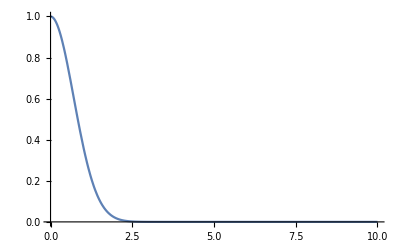

{{f→Function[{p,t},ⅇ^(-(p-t)^2)]}}

ⅇ^(-(-0.01+p)^2)

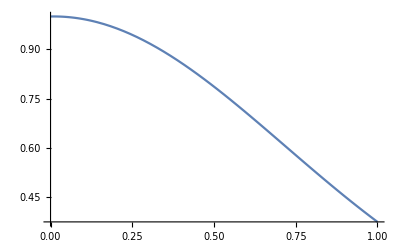

```mathematica
ClearAll["Global`*"]
f0[p_]:=Exp[-p^2];
f0z[z_]:=1;
Plot[f0[p],{p,0,10},PlotRange->Full]
termE1p=D[f[p,t],t]==-1/p^2 D[p^2 f[p,t],p]+2/p f[p,t];
solE1p=DSolve[{termE1p,f[p,0]==f0[p]},f,{p,t}]
t=0.01;
fn=f[p,t]/.solE1p[[1]]
Plot[fn,{p,0,1}]
```

```mathematica
ClearAll["Global`*"];
f0p[p_]:=Exp[-p^2];
f0z[z_]:=Cos[z Pi]+1;
f0[p_,z_]:=f0p[p] f0z[z];
termE1=-EE z/p^2 D[p^2 f[p,z],p];
termE2=-EE/p D[(1-z^2) f[p,z],z];
solE=DSolve[{termE1+termE2==0,f[p,1]==f0[p,1],f[0,z]==f0[0,z]},f,{p,z}];
fn=f[p,z]/.solE[[1]]
ContourPlot[fn,{p,0,1},{z,-1,1},PlotLegends->Automatic]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ReplaceAll::reps: {-(EE (-2 z f[p,z]+(1+Times[«2»]) f^(0,1)[p,z]))/p-(EE z (2 p f[p,z]+p^2 f^(1,0)[p,z]))/p^2==0,f[p,1]==0,f[0,z]==1+Cos[π z]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

f[p,z]/.{-(EE (-2 z f[p,z]+(1-z^2) f^(0,1)[p,z]))/p-(EE z (2 p f[p,z]+p^2 f^(1,0)[p,z]))/p^2==0,f[p,1]==0,f[0,z]==1+Cos[π z]}

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-14000. EE (1.99971 f[0.0000714286,-0.999857]+0.000285694 f^(0,1)[0.0000714286,-0.999857])+1.95972×10^8 EE (0.000142857 f[0.0000714286,-0.999857]+5.10204×10^-9 f^(1,0)[«23»,-«19»])==0.,f[«1»]==«3»,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-13.986 EE (1.99971 f[0.0715,-0.999857]+0.000285694 f^(0,1)[0.0715,-0.999857])+195.581 EE (0.143 f[0.0715,-0.999857]+0.00511225 f^(1,0)[0.0715,-0.999857])==0,f[0.0715,1]==0,f[0,-0.999857]==1.0071×10^-7} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

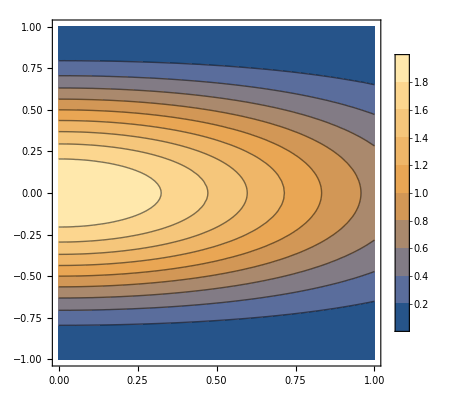

DSolve::dvlen: The function f[p,z,t] does not have the same number of arguments as independent variables (2).

DSolve[{-(0.25 (-2 z f[p,z,t]+(1-z^2) f^(0,1,0)[p,z,t]))/p-(0.25 z (2 p f[p,z,t]+p^2 f^(1,0,0)[p,z,t]))/p^2==0,f[0,z]==1+Cos[π z]},f,{p,z}]

ReplaceAll::reps: {-(0.25 (-2 z f[p,z,t]+(1+Times[«2»]) f^(0,1,0)[p,z,t]))/p-(0.25 z (2 p f[p,z,t]+p^2 f^(1,0,0)[p,z,t]))/p^2==0,f[0,z]==1+Cos[π z]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

f[p,z]/.{-(0.25 (-2 z f[p,z,t]+(1-z^2) f^(0,1,0)[p,z,t]))/p-(0.25 z (2 p f[p,z,t]+p^2 f^(1,0,0)[p,z,t]))/p^2==0,f[0,z]==1+Cos[π z]}

ReplaceAll::reps: {-3500. (1.99971 f[0.0000714286,-0.999857,t]+0.000285694 f^(0,1,0)[0.0000714286,-0.999857,t])+4.8993×10^7 (0.000142857 f[0.0000714286,-0.999857,t]+5.10204×10^-9 f^(«1»)[«23»,-«19»,t])==0,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-3500. (1.99971 f[0.0000714286,-0.999857,t]+0.000285694 f^(0,1,0)[0.0000714286,-0.999857,t])+4.8993×10^7 (0.000142857 f[0.0000714286,-0.999857,t]+5.10204×10^-9 f^(«1»)[«23»,-«19»,t])==0.,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-3.4965 (1.99971 f[0.0715,-0.999857,t]+0.000285694 f^(0,1,0)[0.0715,-0.999857,t])+48.8952 (0.143 f[0.0715,-0.999857,t]+0.00511225 f^(1,0,0)[0.0715,-0.999857,t])==0,f[0,-0.999857]==1.0071×10^-7} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable p. Artificial boundary effects may be present in the solution.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable z. Artificial boundary effects may be present in the solution.

NDSolve::eerr: Warning: scaled local spatial error estimate of 250.603 at t = 1. in the direction of independent variable z is much greater than the prescribed error tolerance. Grid spacing with 23 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{f→InterpolatingFunction[…]}}

```mathematica
ClearAll["Global`*"];
f0p[p_]:=Exp[-p^2];
f0z[z_]:=Cos[z Pi]+1;
f0[p_,z_]:=f0p[p] f0z[z];
EE = 0.25;
ContourPlot[f0[p,z],{p,0,1},{z,-1,1},PlotLegends->Automatic]
termE1=-EE z/p^2 D[p^2 f[p,z,t],p];
termE2=-EE 1/p D[(1-z^2) f[p,z,t],z];
solE=DSolve[{termE1+termE2==0,f[0,z]==f0z[z]},f,{p,z}]
fn=f[p,z]/.solE[[1]]
ContourPlot[fn,{p,0,1},{z,-1,1},PlotLegends->Automatic]
int=NDSolve[{D[f[p,z,t],t]==termE1+termE2,f[p,z,0]==f0[p,z]},f,{p,0.1,1},{z,-1,1},{t,0,1}]
```

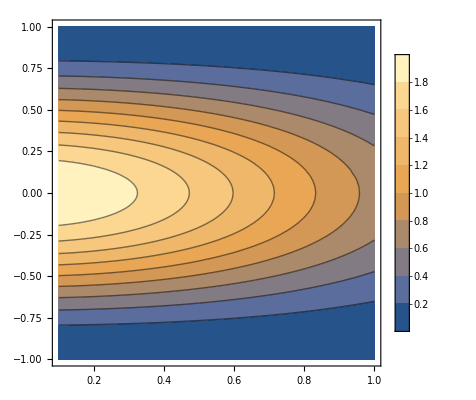

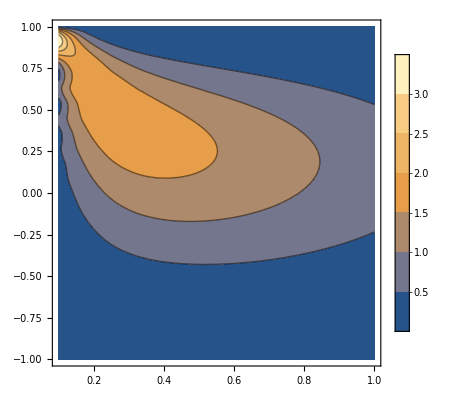

```mathematica
t=0.0;
ContourPlot[Evaluate[f[p,z,t]/.int],{p,0.1,1},{z,-1,1},PlotLegends->Automatic]
t=0.5;
ContourPlot[Evaluate[f[p,z,t]/.int],{p,0.1,1},{z,-1,1},PlotLegends->Automatic]
```